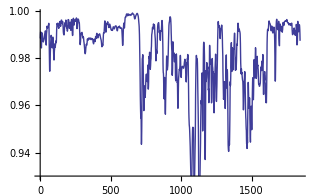

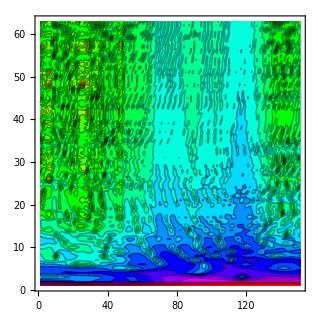

```mathematica
ClearAll[file,x]
(*file=(Import["P:/mhh/00506534.ASC.csv.head.csv","Data","HeaderLines"->0]);*)
file=(Import["m:\\andre-work\\test.csv","Data","HeaderLines"->0]);
fft=(Import["M:\\Proband1\\00506534Schluck7.ASC.data\\result.csv","Data","HeaderLines"->0]);
data=(Import["M:\\Proband1\\00506534Schluck7.ASC.data\\data.csv","Data","HeaderLines"->0]);


ListPlot[MovingAverage[file[[All,2]],5],Joined->True]
(*ListContourPlot[data[[All,5;;9]]//Transpose, Contours->20,PlotRange->All,ColorFunction->Hue]*)
ListContourPlot[fft[[79;;229,2;;64]]//Transpose, Contours->20,PlotRange->All,ColorFunction->Hue]


(*ParallelTable[ListPlot[file[[All,x]],PlotLabel->StringJoin["Column ",ToString[x], " (full range)"], Joined->True,PlotRange->All],{x,2,28}]*)
(*ParallelTable[ListPlot[file[[All,x]],PlotLabel->StringJoin["Column ",ToString[x]], Joined->True],{x,2,28}]*)
```